g2 graph 21b
level 4

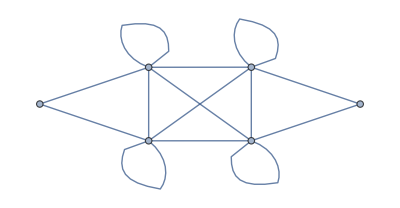

```mathematica
(*SetDirectory["~/Documents/UNH/Research/code/OTimes/graph_21b"];*)

level=4;
q=Exp[Pi*I/(3*(4+level))];
quan[n_,q_]:=(q^n-q^-n)/(q-q^-1)
inDeg[x_]:=360*Arg[x]/(2Pi)

gammaAdj = { 
{0,1,0,0,0,1},
{1,1,1,0,1,1},
{0,1,1,1,1,1},
{0,0,1,0,1,0},
{0,1,1,1,1,1},
{1,1,1,0,1,1}
 };
Clear[aa,bb,cc,dd,ee,ff,gg,hh,ii,jj,kk,ll,mm,nn,oo,pp,qq,rr,ss,tt,uu,vv,ww,xx];
SetNonCommutative[aa,bb,cc,dd,ee,ff,gg,hh,ii,jj,kk,ll,mm,nn,oo,pp,qq,rr,ss,tt,uu,vv,ww,xx];
gammaSym = { 
{0,aa,0,0,0,bb},
{cc,dd,ee,0,ff,gg},
{0,hh,ii,jj,kk,ll},
{0,0,mm,0,nn,0},
{0,oo,pp,qq,rr,ss},
{tt,uu,vv,0,ww,xx}
};
 (* see physics paper *)
loopParam = FullSimplify[q^10+q^8+q^2+1+q^-2+q^-8+q^-10];
delta=loopParam;
AdjacencyGraph[ gammaAdj] (* picture of the graph *)

Hom3to3 = GetHomBasisList[gammaSym, 3,3];
dim3to3 = Length[Hom3to3];
Hom2to4 = GetHomBasisList[gammaSym, 2,4];
dim2to4 = Length[Hom2to4];
Hom4to4 = GetHomBasisList[gammaSym, 4,4];
dim4to4 = Length[Hom4to4];
Hom4to2 = GetHomBasisList[gammaSym, 4,2];
dim4to2 = Length[Hom4to2];
Hom4to1 = GetHomBasisList[gammaSym, 4,1];
dim4to1 = Length[Hom4to1];
Hom2to3 = GetHomBasisList[gammaSym, 2,3];
dim2to3 = Length[Hom2to3];
Hom2to2 = GetHomBasisList[gammaSym,2,2];
dim2to2 = Length[Hom2to2];
Hom2to1 = GetHomBasisList[gammaSym,2,1];
dim2to1 = Length[Hom2to1];
Hom2to0 = GetHomBasisList[gammaSym,2,0];
dim2to0 = Length[Hom2to0];
Hom1to2 = GetHomBasisList[gammaSym,1,2];
dim1to2 = Length[Hom1to2];
Hom1to1 = GetHomBasisList[gammaSym,1,1];
dim1to1 = Length[Hom1to1];
Hom1to0 = GetHomBasisList[gammaSym,1,0];
dim1to0 = Length[Hom1to0];
Hom0to1 = GetHomBasisList[gammaSym,0,1];
dim0to1 = Length[Hom0to1];
Hom0to0 = GetHomBasisList[gammaSym,0,0];
dim0to0 = Length[Hom0to0];
Hom0to2 = GetHomBasisList[gammaSym, 0,2];
dim0to2 = Length[Hom0to2];
Hom0to4 = GetHomBasisList[gammaSym, 0,4];
dim0to4 = Length[Hom0to4];
Hom4to0 = GetHomBasisList[gammaSym, 4,0];
dim4to0 = Length[Hom4to0];

Stick = GenerateStick[gammaAdj, gammaSym];
DoubleStick = InTermsOf[Tens[{Stick, Stick}], Hom2to2];
```